12 Derivadas
12.1 Integrales indefinidas

```mathematica
Integrate[x^5,x]
```

x^6/6

```mathematica
Integrate[4y^3-5y,y]
```

-(5 y^2)/2+y^4

```mathematica
Integrate[x*Cos[x],x]
D[Cos[x]+x Sin[x],x]
```

Cos[x]+x Sin[x]

x Cos[x]

```mathematica
Integrate[Exp[-x^2],x] (* En términos de la función error *)
```

1/2 √π Erf[x]

```mathematica
Integrate[Sin[x]/x,x] (* No existe en los reales *)
```

SinIntegral[x]

12.2 Integrales definidas

```mathematica
Integrate[4x^3-4x,{x,0,4}]
```

224

```mathematica
Integrate[Cos[x],{x,0,Pi/2}]
```

1

```mathematica
Integrate[Sin[x]/x,{x,0,4}]
NIntegrate[Sin[x]/x,{x,0,4},WorkingPrecision->20] (* Integral numérica *)
```

SinIntegral[4]

1.7582031389490530581

12.3 Integrales impropias

```mathematica
Integrate[1/x,{x,1,Infinity}]
```

Integrate::idiv: Integral of 1/x does not converge on {1,∞}.

∫_1^∞ 1/x ⅆx

```mathematica
Integrate[1/Sqrt[x],{x,0,6}]
```

2 √6

```mathematica
Integrate[Exp[-x^2],{x,-Infinity,Infinity}]
```

√π

```mathematica
Integrate[1/x^2,{x,-2,2}]
```

Integrate::idiv: Integral of 1/x^2 does not converge on {-2,2}.

∫_-2^2 1/x^2 ⅆx

12.4 Integrales de fracciones algebraicas

```mathematica
Apart[(5x+3)/(x^2+2x-3)]
```

2/(-1+x)+3/(3+x)

```mathematica
Integrate[%,x]
```

2 Log[-1+x]+3 Log[3+x]

```mathematica
Integrate[(5x+3)/(x^2+2x-3),x]
```

2 Log[1-x]+3 Log[3+x]

12.5 Integrales dependientes de parámetros

```mathematica
Integrate[A*Cos[w*t],t]
```

(A Sin[t w])/w

12.6 Cálculo de áreas

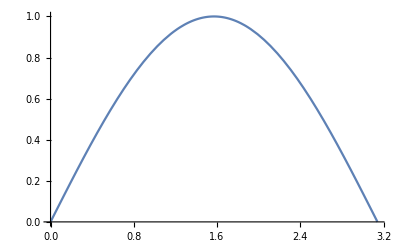

```mathematica
Plot[Sin[x],{x,0,Pi}]
```

```mathematica
Integrate[Sin[x],{x,0,Pi}]
```

2

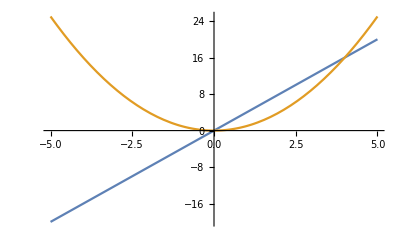

```mathematica
Plot[{4x,x^2},{x,-5,5}]
```

```mathematica
Solve[4x==x^2,x] (* Puntos de intersección *)
```

{{x→0},{x→4}}

```mathematica
Integrate[4x-x^2,{x,0,4}] (* Área entre las curvas *)
```

32/3

12.7 Sumas de series numéricas
a) ∑_(n=1)^100 n
b) ∑_(i=1)^n i
c) ∑_(i=1)^n i^2
d) ∑_(n=1)^∞ 1/n^2
e) ∑_(n=1)^∞ 1/n

```mathematica
Sum[n,{n,1,100}] (* a) *)
```

5050

```mathematica
Sum[i,{i,1,n}] (* b) *)
```

1/2 n (1+n)

```mathematica
Sum[i^2,{i,1,n}] (* c) *)
```

1/6 n (1+n) (1+2 n)

```mathematica
Sum[1/n^2,{n,1,Infinity}] (* d) *)
```

π^2/6

```mathematica
Sum[1/n,{n,1,Infinity}] (* e) *)
Sum[1/n,{n,1,10}]//N
Sum[1/n,{n,1,1000}]//N
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/n

2.92897

7.48547